# 08. Time-Dependent Hamiltonians and MAS Optimal Control

## PeriodicFunction magic-angle spinning drifts, CF4 commutator-free Magnus integration, rotor-phase-invariant recoupling, and post-pulse Signal1D COMPUTE verification.

## 0. Setup and Loading SpinDynamica

Add the SpinDynamica package directory to $Path by searching upward from the notebook directory and load SpinDynamica`. All five OptimalControl` subpackages load automatically. Reuses Examples/OptimalControl/Tutorials/Tutorial09_MASOptimalControl.wls (Manual Chapter 18).

```mathematica
Module[{dir = Quiet[Check[NotebookDirectory[], Directory[]]], found = None},
  Do[If[FileExistsQ[FileNameJoin[{dir, "SpinDynamica", "SpinDynamica.m"}]],
      found = FileNameJoin[{dir, "SpinDynamica"}]; Break[]];
    dir = ParentDirectory[dir], {6}];
  If[found === None && FileExistsQ[FileNameJoin[{Directory[], "SpinDynamica", "SpinDynamica.m"}]],
    found = FileNameJoin[{Directory[], "SpinDynamica"}]];
  If[StringQ[found] && !MemberQ[$Path, found], PrependTo[$Path, found]];
];
Needs["SpinDynamica`"];
<|"Version" -> $SpinDynamicaVersion, "OptimalControlContexts" -> Select[$Packages, StringStartsQ[#, "OptimalControl`"] &]|>
```

SpinDynamica version SDv3.10.3b3 (modified by Google Anti-Gravity Neon) loaded by Mathematica 14.3 running on Microsoft Windows (64-bit).

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator,Duration,Exp,Expand,Plus,Power,Simplify,SolidAngle,Times,WignerD}

<|Version→SDv3.10.3b3 (modified by Google Anti-Gravity Neon),OptimalControlContexts→{OptimalControl`Visualization`,OptimalControl`TimeOptimal`,OptimalControl`SecondOrderOptimizers`,OptimalControl`Optimizers`,OptimalControl`Ensemble`,OptimalControl`GRAPE`,OptimalControl`Objectives`,OptimalControl`Kernels`}|>

## Introduction

In solid-state NMR under magic-angle spinning (MAS) at spinning rate nu_r = 1/T_r, anisotropic interactions such as dipolar couplings and chemical-shift anisotropy (CSA) become periodically time-dependent: H_0(t + T_r) = H_0(t). Designing recoupling pulses across rotor periods requires fourth-order integration of H_0(t) inside every RF slice alongside ensemble averaging over unknown crystallite rotor starting phases t0.

Construct continuous time-dependent drifts via SpinDynamica's PeriodicFunction.

Compare DriftIntegration accuracy across Midpoint, SubSlices, CF4 (GaussLegendre2), and refined CF4x2 / CF4x4 schemes.

Verify analytical CF4 gradients against central finite differences.

Optimise rotor-phase-invariant dipolar recoupling (sweeping InitialTimePoint -> t0Sym) and feed the result into Signal1D "COMPUTE".

## Mathematical Background

On each piecewise-constant control slice [t_{j-1}, t_j) of width h = dt_j, default DriftIntegration -> "CF4" (fourth-order two-stage Commutator-Free Magnus integrator) evaluates H_0(t) once during compilation at Gauss-Legendre nodes t_{1,2} = t_{j-1} + h (1/2 -/+ Sqrt[3]/6) and advances by U_{j} = U_{j,2} U_{j,1} using weights w_+- = 1/2 +/- Sqrt[3]/3.

All five GRAPE kernels operate transparently over N_fine = N_t * nStages fine stages while broadcasting constant RF amplitudes u_{j,k}. Note carefully: Signal1D[..., SignalCalculationMethod -> "COMPUTE"] accelerates periodic acquisition under static events ({None, dur}), whereas GRAPEOptimize handles active shaped RF irradiation using CF4 time-domain propagation.

## Worked Example

Execute Tutorial 09: build a 10 kHz (T_r = 100 us) MAS dipolar + CSA Hamiltonian Hdip via PeriodicFunction, measure propagator convergence vs CF4x4, check CF4 gradient accuracy, optimise a 4-rotor-phase invariant recoupling pulse over 2 T_r, and verify both VerifyOptimalControlSimulation and post-pulse Signal1D "COMPUTE" vs "Direct".

```mathematica
SetSpinSystem[{{1, 1/2}, {2, 1/2}}];
b2 = ZeemanBasis[];
ctrls4 = {opI[1, "x"], opI[1, "y"], opI[2, "x"], opI[2, "y"]};
trMAS = 1./10000.;
wr = 2. Pi / trMAS;
Hdip = PeriodicFunction[t, trMAS, Evaluate[
  1500. * opI[1, "z"] - 3500. * opI[2, "z"] + 4000. * Cos[wr t] * opI[1, "z"] +
  6000. * (Cos[wr t] + 0.5 Sin[2 wr t]) * (2 opI[1, "z"].opI[2, "z"] - opI[1, "x"].opI[2, "x"] - opI[1, "y"].opI[2, "y"])
]];

(* 1. Quadrature convergence & CF4 gradient check *)
SeedRandom[90]; uProbe = RandomReal[{-3000., 3000.}, {12, 4}];
props = AssociationThread[{"Midpoint", "SubSlices4", "CF4", "CF4x2", "CF4x4"} -> Map[Function[s,
  EvaluateOptimalControl[OptimalControlProblem[Hdip, ctrls4, StateTarget[opI[1, "z"] -> opI[2, "z"]],
    {2. * trMAS, 12}, InitialTimePoint -> trMAS/4., FrequencyUnits -> "Hz", ControlUnits -> "Hz", DriftIntegration -> s],
    uProbe]["FinalPropagator"]], {"Midpoint", {"SubSlices", 4}, "CF4", {"CF4", 2}, {"CF4", 4}}]];
convErrs = Max[Abs[# - props["CF4x4"]]] & /@ KeyDrop[props, "CF4x4"];
gradCF4 = VerifyOptimalControlGradient[OptimalControlProblem[Hdip, ctrls4, StateTarget[opI[1, "z"] -> opI[2, "z"]],
  {2. * trMAS, 12}, InitialTimePoint -> trMAS/4., FrequencyUnits -> "Hz", ControlUnits -> "Hz", DriftIntegration -> "CF4"],
  uProbe, StepSize -> 0.05];

(* 2. 4-Rotor-phase invariant dipolar recoupling & post-pulse Signal1D COMPUTE check *)
ensMAS = OptimalControlEnsemble[Hdip, ctrls4, StateTarget[opI[1, "z"] -> opI[2, "z"]], {2. * trMAS, 24},
  EnsembleParameters -> {t0Sym -> {0., trMAS/4., trMAS/2., 3. * trMAS/4.}},
  InitialTimePoint -> t0Sym, FrequencyUnits -> "Hz", ControlUnits -> "Hz", DriftIntegration -> {"CF4", 2}];
resMAS = GRAPEOptimize[ensMAS, AmplitudeNormBound -> 18000., TargetFidelity -> 0.995, MaxIterations -> 140, RandomSeed -> 77];
simMAS = VerifyOptimalControlSimulation[resMAS, Tolerance -> 10^-5];
rhoAfter = NPropagate[OptimalControlEventList[resMAS, IncludeDrift -> False], Basis -> b2, BackgroundGenerator -> Hdip, InitialTimePoint -> 0.][opI[1, "z"]];
sigComp = Quiet[Signal1D[{0, 3 trMAS, trMAS/4.}, {None, 3 trMAS}, InitialDensityOperator -> rhoAfter, Observable -> opI[2, "z"],
  BackgroundGenerator -> Hdip, InitialTimePoint -> 2. * trMAS, SignalCalculationMethod -> "COMPUTE", LineBroadening -> None, DigitalFrequencyResolution -> False]];
sigDir = Quiet[Signal1D[{0, 3 trMAS, trMAS/4.}, {None, 3 trMAS}, InitialDensityOperator -> rhoAfter, Observable -> opI[2, "z"],
  BackgroundGenerator -> Hdip, InitialTimePoint -> 2. * trMAS, SignalCalculationMethod -> "Direct", LineBroadening -> None]];
sigErr = Max[Abs[(Last /@ Expand[sigComp]) - (Last /@ Expand[sigDir])]];

<|"QuadratureErrorsVsCF4x4" -> convErrs, "CF4_GradPassed" -> gradCF4["PassedQ"],
  "MAS_MeanF" -> resMAS["MeanMemberFidelity"], "MAS_MinF" -> resMAS["MinMemberFidelity"],
  "MAS_SDMatch" -> simMAS["FidelityMatchQ"], "Signal1D_ComputeVsDirectErr" -> sigErr|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

<|QuadratureErrorsVsCF4x4→<|Midpoint→0.0410367,SubSlices4→0.0026729,CF4→0.00109645,CF4x2→0.0000517119|>,CF4_GradPassed→True,MAS_MeanF→0.995723,MAS_MinF→0.993851,MAS_SDMatch→True,Signal1D_ComputeVsDirectErr→2.67087×10^-8|>

Visualise the MAS recoupling waveform and rotor-phase member fidelities:

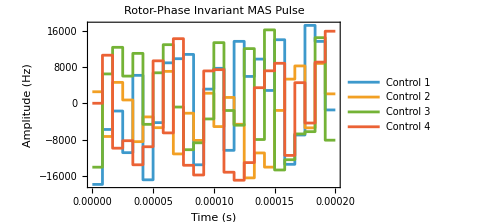
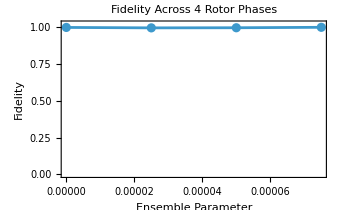
-Graphics- | -Graphics-

```mathematica
Grid[{{
  PlotOptimalControlWaveform[resMAS, PlotLabel -> "Rotor-Phase Invariant MAS Pulse", ImageSize -> 360],
  PlotEnsembleFidelity[resMAS, PlotLabel -> "Fidelity Across 4 Rotor Phases", ImageSize -> 340]
}}]
```

## Interactive Exploration

Lab 8A instantaneously explores MAS DriftIntegration accuracy across spinning frequency nu_r, dipolar strength, slices per rotor period, and rotor starting phase t0/Tr (forward-only comparison against CF4x4, zero optimisation).

```mathematica
renderLab8A[nuRKHz_?NumericQ, dKHz_?NumericQ, slicesPerTr_Integer, fracT0_?NumericQ] := Module[
  {ctrls4, tr, wr, tVar, hMod, nt, t0, uTest, refU, schemes, errs, names},
 Quiet@SetSpinSystem[{{1, 1/2}, {2, 1/2}}];
  ctrls4 = {opI[1, "x"], opI[1, "y"], opI[2, "x"], opI[2, "y"]};
  tr = 1. / (1000. * nuRKHz); wr = 2. Pi / tr;
  hMod = PeriodicFunction[tVar, tr, Evaluate[
    1500. * opI[1, "z"] - 3500. * opI[2, "z"] +
    (1000. * dKHz) * (Cos[wr tVar] + 0.5 Sin[2 wr tVar]) * (2 opI[1, "z"].opI[2, "z"] - opI[1, "x"].opI[2, "x"] - opI[1, "y"].opI[2, "y"])
  ]];
  nt = 2 * slicesPerTr; t0 = fracT0 * tr;
  SeedRandom[90]; uTest = RandomReal[{-3000., 3000.}, {nt, 4}];
  refU = EvaluateOptimalControl[OptimalControlProblem[hMod, ctrls4, StateTarget[opI[1, "z"] -> opI[2, "z"]],
    {2. * tr, nt}, InitialTimePoint -> t0, FrequencyUnits -> "Hz", ControlUnits -> "Hz", DriftIntegration -> {"CF4", 4}], uTest]["FinalPropagator"];
  schemes = {"Midpoint", {"SubSlices", 2}, {"SubSlices", 4}, "CF4", {"CF4", 2}};
  names = {"Midpoint", "SubSlices(2)", "SubSlices(4)", "CF4", "CF4(2)"};
  errs = Map[Function[s, Max[Abs[EvaluateOptimalControl[
    OptimalControlProblem[hMod, ctrls4, StateTarget[opI[1, "z"] -> opI[2, "z"]], {2. * tr, nt},
      InitialTimePoint -> t0, FrequencyUnits -> "Hz", ControlUnits -> "Hz", DriftIntegration -> s], uTest]["FinalPropagator"] - refU]]], schemes];
  Column[{
    Row[{"nu_r = ", nuRKHz, " kHz (Tr = ", NumberForm[10^6 tr, 4], " us)   D = ", dKHz, " kHz   Nt = ", nt, " (", slicesPerTr, "/Tr)"}],
    BarChart[Max[#, 10^-9] & /@ errs, ScalingFunctions -> "Log", ChartLabels -> names, Frame -> True,
      FrameLabel -> {None, "Max Propagator Error vs CF4(4)"}, PlotRange -> {10^-6, 1.}, ImageSize -> 470]
  }]
];

runLab8B[nuRKHz_, nRotors_Integer, nPhases_Integer, intMode_, rfMaxKHz_] := Module[
  {ctrls4, tr, wr, tVar, hMod, t0Vals, nt, ens, res, sim},
 Quiet@SetSpinSystem[{{1, 1/2}, {2, 1/2}}];
  ctrls4 = {opI[1, "x"], opI[1, "y"], opI[2, "x"], opI[2, "y"]};
  tr = 1. / (1000. * nuRKHz); wr = 2. Pi / tr;
  hMod = PeriodicFunction[tVar, tr, Evaluate[
    1500. * opI[1, "z"] - 3500. * opI[2, "z"] + 4000. * Cos[wr tVar] * opI[1, "z"] +
    6000. * (Cos[wr tVar] + 0.5 Sin[2 wr tVar]) * (2 opI[1, "z"].opI[2, "z"] - opI[1, "x"].opI[2, "x"] - opI[1, "y"].opI[2, "y"])
  ]];
  t0Vals = Table[(k - 1.) * tr / nPhases, {k, nPhases}];
  nt = 12 * nRotors;
  ens = OptimalControlEnsemble[hMod, ctrls4, StateTarget[opI[1, "z"] -> opI[2, "z"]], {nRotors * tr, nt},
    EnsembleParameters -> {t0Sym -> t0Vals}, InitialTimePoint -> t0Sym,
    FrequencyUnits -> "Hz", ControlUnits -> "Hz", DriftIntegration -> intMode];
  res = GRAPEOptimize[ens, AmplitudeNormBound -> (1000. * rfMaxKHz), TargetFidelity -> 0.995, MaxIterations -> 100, RandomSeed -> 77];
  sim = VerifyOptimalControlSimulation[res, Tolerance -> 10^-4];
  <|"Result" -> res, "Sim" -> sim, "NuRKHz" -> nuRKHz, "NRotors" -> nRotors, "NPhases" -> nPhases, "IntMode" -> intMode|>
];

renderLab8B[d_Association] := Module[{res = d["Result"]},
  Column[{
    Panel[Row[{"nu_r = ", d["NuRKHz"], " kHz   Dur = ", d["NRotors"], " Tr   Rotor Phases = ", d["NPhases"],
      "   Int = ", d["IntMode"], "   MeanF = ", NumberForm[res["MeanMemberFidelity"], 5],
      "   MinF = ", NumberForm[res["MinMemberFidelity"], 5], "   SDMatch = ", d["Sim"]["FidelityMatchQ"]}]],
    Row[{
      PlotOptimalControlWaveform[res, ImageSize -> 350],
      PlotEnsembleFidelity[res, ImageSize -> 310]
    }]
  }]
];

lab8BDefault = runLab8B[10., 2, 4, "CF4", 18.];
{lab8BDefault["Result"]["MeanMemberFidelity"], lab8BDefault["Result"]["MinMemberFidelity"]}
```

{0.995407,0.994005}

```mathematica
Manipulate[
  renderLab8A[nuRKHz, dKHz, slicesPerTr, fracT0],
  {{nuRKHz, 10., "MAS Rate nu_r (kHz)"}, 5., 25., 2.5, Appearance -> "Labeled"},
  {{dKHz, 6., "Dipolar Coupling D (kHz)"}, 2., 12., 1., Appearance -> "Labeled"},
  {{slicesPerTr, 6, "Slices per Rotor Period"}, {4, 6, 8, 12}},
  {{fracT0, 0.25, "Start Rotor Phase t0/Tr"}, 0., 1., 0.125, Appearance -> "Labeled"},
  ContinuousAction -> False
]
```

Lab 8B optimises rotor-phase-invariant MAS dipolar recoupling on demand via queued evaluation:

```mathematica
DynamicModule[{nuR = 10., nRot = 2, nPh = 4, intM = "CF4", rfKHz = 18., data = lab8BDefault},
  Panel[Column[{
    Grid[{
      {"MAS Rate (kHz)", SetterBar[Dynamic[nuR], {8., 10., 15.}]},
      {"Duration (Rotor Periods)", SetterBar[Dynamic[nRot], {1, 2, 3}]},
      {"Rotor-Phase Sweep Size", SetterBar[Dynamic[nPh], {1, 2, 4}]},
      {"DriftIntegration", SetterBar[Dynamic[intM], {"Midpoint", "CF4", {"CF4", 2}}]},
      {"RF Disk Limit (kHz)", Row[{Slider[Dynamic[rfKHz], {10., 25., 1.}], " ", Dynamic[rfKHz]}]}
    }, Alignment -> Left],
    Button["Run MAS Recoupling", data = runLab8B[nuR, nRot, nPh, intM, rfKHz], Method -> "Queued"],
    Dynamic[renderLab8B[data]]
  }]]
]
```

## Suggested Experiments

1. Observe fourth-order accuracy: In Lab 8A, reduce Slices per Rotor Period to 4. Notice how single-step CF4 already beats 4x-more-expensive SubSlices(4) while cutting Midpoint error by > 10x.

2. Rotor-phase collapse: In Lab 8B, set Rotor-Phase Sweep Size = 1 vs 4. A single-phase recoupling pulse can easily fail when crystallites start 90 degrees or 180 degrees out of phase; sweeping 4 rotor phases forces gamma-like robustness.

3. Underpowered recoupling: Drop RF Disk Limit down to 10 kHz at nu_r = 15 kHz and observe how Hartmann-Hahn / R-sequence amplitude bottlenecks affect recoupling efficiency.

4. Compare VerifyOptimalControlSimulation under "Midpoint" vs "CF4" on fast spinning rates (15 kHz).

## Summary

PeriodicFunction combined with fourth-order CF4 DriftIntegration and symbolic InitialTimePoint sweeps brings exact-gradient optimal control cleanly to MAS solid-state NMR dipolar recoupling, integrating seamlessly downstream with NPropagate and periodic Signal1D "COMPUTE".

Return to 00_OptimalControl_Tutorials_Index.nb or consult the executable CLI fixture (Tutorial09_MASOptimalControl.wls) and Manual Ch. 18.